```mathematica
Naloga 1:
```

```mathematica
izraz=(x^5-2x^2+3x+4)/(x^5-2x-1)
```

(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)

```mathematica
izraz/.x->1
```

-3

```mathematica
izraz/.x->2
```

34/27

```mathematica
izraz/.x->3
```

119/118

```mathematica
izraz/.x->4
```

144/145

```mathematica
izraz/.x->{1,2,3,4,5}
```

{-3,34/27,119/118,144/145,1547/1557}

```mathematica
f[x_]=(x^5-2x^2+3x+4)/(x^5-2x-1)
```

(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)

```mathematica
f[3]
```

119/118

```mathematica
f[0]
```

-4

```mathematica
f[-2]
```

42/29

```mathematica
Table[f[x],{x,1,10,1}]
```

```mathematica
{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

```mathematica
Map[f,{1,2,8,13}]
```

{-3,34/27,32668/32751,185499/185633}

```mathematica
Naloga 2:
```

```mathematica
sez={10,20,30,40,50,60,70}
```

{10,20,30,40,50,60,70}

```mathematica
Take[sez,{1,3}]
```

{10,20,30}

```mathematica
Drop[sez,{2,4}]
```

{10,50,60,70}

Naloga 3:

```mathematica
sez = {x^6, x^2, a}
```

{x^6,x^2,a}

```mathematica
ReplaceAll[sez, x->3]
```

{729,9,a}

```mathematica
ReplaceAll[sez, x->x^2]
```

{x^12,x^4,a}

```mathematica
ReplaceAll[sez, x^2 -> x]
```

{x^6,x,a}

```mathematica
ReplaceAll[sez, x->{1,2,3}]
```

{{1,64,729},{1,4,9},a}

```mathematica
ReplaceAll[sez, {x->3, a->x}]
```

{729,9,x}

```mathematica
ReplaceRepeated[sez, {x->3, a->x}]
```

{729,9,3}

```mathematica
sez1 = ReplaceAll[sez, {x->1, x->2, x->3}]
```

{1,1,a}

Naloga 4:

```mathematica
f[x_]:=x^5 + 4 x^3 -9
```

```mathematica
D[f[x],x]
```

12 x^2+5 x^4

```mathematica
D[f[x],x] /. {x->1}
```

17

```mathematica
D[f[x],x] /. {x->5}
```

3425

```mathematica
g[x_]:=E^((x)^(1/4))
```

```mathematica
D[g[x],x]
```

(ⅇ^(x^(1/4)))/(4 x^(3/4))

```mathematica
D[g[x],x]/.{x->1}
```

ⅇ/4

```mathematica
D[g[x],x]/.{x->2}
```

(ⅇ^(2^(1/4)))/(4 2^(3/4))

```mathematica
h[x_]:=Abs[x+1]
```

```mathematica
FullSimplify[D[h[x],x]]
```

Abs'[1+x]

```mathematica
FullSimplify[D[h[x],x]]/.{x->1}
```

Abs'[2]

```mathematica
FullSimplify[D[h[x],x]]/.{x->-1}
```

Abs'[0]

```mathematica
i[x_]:=a x^2 + 3b
```

```mathematica
D[i[x],x]
```

2 a x

```mathematica
D[i[x],x]/.{x->1}
```

2 a

```mathematica
D[i[x],x]/.{x->2}
```

4 a

Naloga 5:

```mathematica
f[x_]:=x^3 Log[4 x + 5]
```

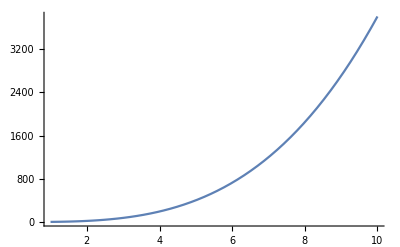

```mathematica
Plot[f[x],{x,1,10},PlotRange->All]
```

```mathematica
f[x] /. {x->5}
```

125 Log[25]

```mathematica
x0=5
```

5

```mathematica
f[5] //N
```

402.359

```mathematica
k=D[f[x],x]/.{x->x0}
```

20+75 Log[25]

```mathematica
k//N
```

261.416

```mathematica
enacba=y==k x+n
```

y==n+x (20+75 Log[25])

```mathematica
enacba2= enacba/.{x->x0, y->f[x0]}
```

125 Log[25]==n+5 (20+75 Log[25])

```mathematica
resitev=Solve[enacba2,n]
```

{{n→-50 (2+5 Log[25])}}

```mathematica
pravilo=First[resitev]
```

{n→-50 (2+5 Log[25])}

```mathematica
n0=n/.pravilo
```

-50 (2+5 Log[25])

```mathematica
Solve[y==k x+n/.{x->x0, y->f[x0]}, n]
```

{{n→-50 (2+5 Log[25])}}

```mathematica
p[x_]:=k*x+n0
```

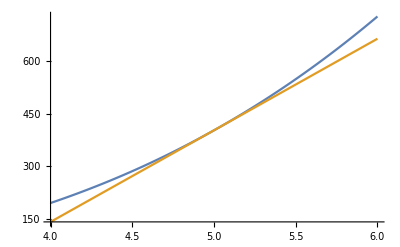

```mathematica
Plot[{f[x],p[x]}, {x,4,6}]
```

Naloga 6:

```mathematica
Limit[(x^3-4x^2+2x+4)/(x^5-9x-14), x->2]
```

-2/71

```mathematica
Limit[ArcTan[7x] / ArcTan[8x], x->0]
```

7/8

```mathematica
Limit[(x^2-25)*Cot[Pi x],x->5]
```

10/π

```mathematica
Limit[(1+Cos[x])/(2(Pi x)^(1/2)-Pi-x), x->Pi]
```

-2 π

```mathematica
Limit[Abs[x]*Cot[x],x->0]
```

Indeterminate

Naloga 7:

```mathematica
f[x_]:=(x^2-1)/(x^2-4)
```

```mathematica
Solve[(x^2-1)==0]
```

{{x→-1},{x→1}}

```mathematica
Solve[(x^2-4)==0]
```

{{x→-2},{x→2}}

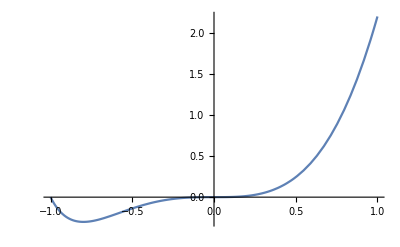

```mathematica
Plot[f[x], {x,-1,1}, PlotRange->All]
```

Naloga 8:

```mathematica
Solve[x^4+x^3-x==0]
```

{{x→0},{x→Root0.755Root[-1+#1^2+#1^3&,1]0.7548776662466927},{x→Root-0.877-0.745 ⅈRoot[-1+#1^2+#1^3&,2]-0.8774388331233465},{x→Root-0.877+0.745 ⅈRoot[-1+#1^2+#1^3&,3]-0.8774388331233465}}